```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["/Users/zackarywindham/Research/Post-Minkowski/build/firstBody.csv"];
x1=#[[2]]&/@data;
y1=#[[3]]&/@data;
z1=#[[4]]&/@data;
x2=#[[5]]&/@data;
y2=#[[6]]&/@data;
z2=#[[7]]&/@data;
body1=Transpose[{x1,y1}];
body2=Transpose[{x2,y2}];
```

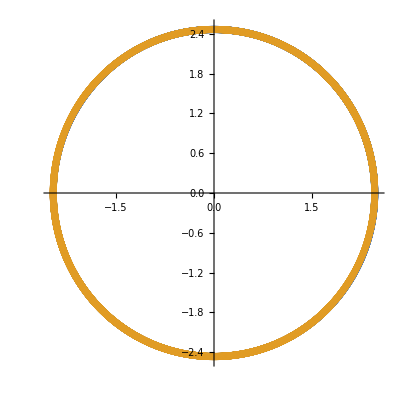

```mathematica
ListPlot[{body1,body2},AspectRatio->1]
```